Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{10.3513,19.8539}

{10.8142,19.8443}

{17.2956,3.52079}

{4.34753,1.84097}

{17.5207,16.4726}

{15.4749,18.1447}

{19.8236,8.27613}

{13.839,19.1465}

{9.46225,0.0602443}

{0.0961557,10.1373}

{4.65093,18.3954}

{0.1658,11.7192}

{8.83319,19.7453}

{6.25919,19.0885}

{2.25224,16.1644}

{19.3383,6.95871}

{18.7213,5.64289}

{15.7737,1.95763}

{0.763992,6.48381}

{19.7829,10.5583}

{1.90788,4.41259}

{6.46538,0.833287}

{12.9027,0.517863}

Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{36.0366,22.1579}

{20.4792,32.9582}

{38.6719,34.8243}

{20.6824,27.1416}

{22.918,23.53}

{39.4069,30.8181}

{29.3217,20.3711}

{24.0007,37.5903}

{36.3964,37.4858}

{34.5014,38.4721}

{38.5591,25.8325}

{30.2437,20.3151}

{35.6585,37.9439}

{39.2291,29.5653}

{20.1194,30.4165}

{27.4466,39.5362}

{20.923,25.9657}

{39.6079,32.6739}

{29.977,39.7782}

{25.5939,21.1223}

{22.144,35.8617}

{34.1438,21.0961}

{39.2316,33.6377}

{{12.9027,0.517863},{6.46538,0.833287},{1.90788,4.41259},{19.7829,10.5583},{0.763992,6.48381},{15.7737,1.95763},{18.7213,5.64289},{19.3383,6.95871},{2.25224,16.1644},{6.25919,19.0885},{8.83319,19.7453},{0.1658,11.7192},{4.65093,18.3954},{0.0961557,10.1373},{9.46225,0.0602443},{13.839,19.1465},{19.8236,8.27613},{15.4749,18.1447},{17.5207,16.4726},{4.34753,1.84097},{17.2956,3.52079},{10.8142,19.8443},{10.3513,19.8539}}

{{39.2316,33.6377},{34.1438,21.0961},{22.144,35.8617},{25.5939,21.1223},{29.977,39.7782},{39.6079,32.6739},{20.923,25.9657},{27.4466,39.5362},{20.1194,30.4165},{39.2291,29.5653},{35.6585,37.9439},{30.2437,20.3151},{38.5591,25.8325},{34.5014,38.4721},{36.3964,37.4858},{24.0007,37.5903},{29.3217,20.3711},{39.4069,30.8181},{22.918,23.53},{20.6824,27.1416},{38.6719,34.8243},{20.4792,32.9582},{36.0366,22.1579}}

{{17.5207,16.4726},{22.918,23.53}}

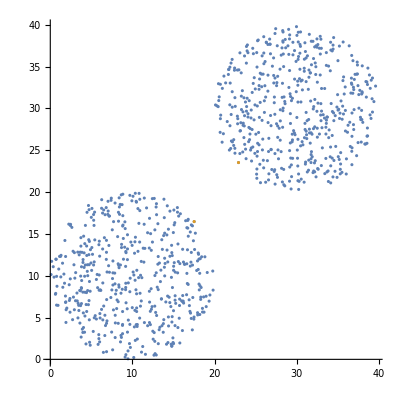

{{17.5207,16.4726},{22.918,23.53}}

-Graphics-

BODY JSOU STEJNE

```mathematica
(*Global Variables*)
numOfPoints = 500;

(*Distributin function for generating point on given region*)
RegionDistribution/:
Random`DistributionVector[RegionDistribution[reg_MeshRegion],n_Integer,prec_?Positive]:=Module[{d=RegionDimension@reg,cells,measures,s,m},cells=Developer`ToPackedArray@MeshPrimitives[reg,d][[All,1]];
s=RandomVariate[DirichletDistribution@ConstantArray[1,d+1],n];
measures=PropertyValue[{reg,d},MeshCellMeasure];
m=RandomVariate[#,n]&@EmpiricalDistribution[measures->Range@Length@cells];
#[[All,1]] (1-Total[s,{2}])+Total[#[[All,2;;]] s,{2}]&@cells[[m]]]

(*Initialize of two regions*)
region1 = DiscretizeRegion@Disk[{10,10},10];
region2 = DiscretizeRegion@Disk[{30, 30}, 10];
pts1= RandomVariate[RegionDistribution[region1],numOfPoints];
pts2= RandomVariate[RegionDistribution[region2],numOfPoints];

area = Join[pts1, pts2];

(*Exctract points on convex hull - both regions*)
convexHullpts1 = RegionBoundary[ConvexHullMesh[pts1]];
convexHullpts2 = RegionBoundary[ConvexHullMesh[pts2]];

arrayOneConvexHull = pts1;
cutConvexHull1[x_]=If[RegionMember[convexHullpts1,arrayOneConvexHull[[x]]],Print[arrayOneConvexHull[[x]]], arrayOneConvexHull = Delete[arrayOneConvexHull, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull1[i]];

arrayTwoConvexHull = pts2;
cutConvexHull2[x_]=If[RegionMember[convexHullpts2,arrayTwoConvexHull[[x]]],Print[arrayTwoConvexHull[[x]]], arrayTwoConvexHull = Delete[arrayTwoConvexHull, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull2[i]];

arrayOneConvexHull
arrayTwoConvexHull

(*Calculate nearest on ConvexHull*)
f = Nearest[arrayOneConvexHull];
c=Flatten[f/@arrayTwoConvexHull,1];
closestPairOnConvexHull = Flatten[Transpose[{c[[#]],arrayTwoConvexHull[[#]]}]&@Ordering[Norm/@(c-arrayTwoConvexHull),1],1]
ListPlot[{area, closestPairOnConvexHull}, AspectRatio->Automatic]

(*Calculate nearest point of two regions*)
r = Nearest[pts1];
d=Flatten[r/@pts2,1];
closestPair = Flatten[Transpose[{d[[#]],pts2[[#]]}]&@Ordering[Norm/@(d-pts2),1],1]
ListPlot[{area, closestPair}, AspectRatio->Automatic]

(*Check if points are the same and if they belong to convex hull*)
If[closestPair == closestPairOnConvexHull,Print["BODY JSOU STEJNE"],
If[(ContainsAny[arrayOneConvexHull, closestPair])&&(ContainsAny[arrayTwoConvexHull, closestPair]),Print["BODY JSOU JINE ALE OBA NA KONVEXNÍ OBÁLCE"], Print["JEDEN NEBO OBA BODY NEJSOU NA KONVEXNÍ OBÁLCE"]]]

(*
(*Calculate nearest on ConvexHull*)
oneToTwoConvexHull = First[Nearest[arrayOneConvexHull,arrayTwoConvexHull]]
Nearest[arrayOneConvexHull,arrayTwoConvexHull]
twoToOneConvexHull = First[Nearest[arrayTwoConvexHull,arrayOneConvexHull]]
Nearest[arrayTwoConvexHull,arrayOneConvexHull]
ListPlot[{area, oneToTwoConvexHull, twoToOneConvexHull}, AspectRatio->Automatic]

(*Calculate nearest point of two regions*)
Nearest[pts1,pts2]
oneToTwo = First[Nearest[pts1,pts2]]
Nearest[pts2,pts1]
twoTo0ne= First[Nearest[pts2,pts1]]
ListPlot[{area, oneToTwo, twoTo0ne}, AspectRatio->Automatic]

(*Check if points are the same and if they belong to convex hull*)
If[(oneToTwo == oneToTwoConvexHull) && (twoTo0ne == twoToOneConvexHull),Print["BODY JSOU STEJNE"],
If[(ContainsAny[arrayOneConvexHull, oneToTwo])&&(ContainsAny[arrayTwoConvexHull, twoTo0ne]),Print["BODY JSOU JINE ALE OBA NA KONVEXNÍ OBÁLCE"]], Print["JEDEN NEBO OBA BODY NEJSOU NA KONVEXNÍ OBÁLCE"] ]*)
```